```mathematica
inecessary={};
```

## Primary definitions

```mathematica
ClearAll["Global`*"]
ParallelEvaluate[ClearAll["Global`*"]];
CloseKernels[];
LaunchKernels[];
<<FeynCalc`
(*{indexenergy,indexmass,indexpx,indexpy,indexpz,indexpm,indexcθ,indexpdec,indexxdec,indexydec,indexzdec,indexazacc}=Range[1,12];*)
inecessary={};
DirectoryRoutinesEventCalc=FileNameJoin[{NotebookDirectory[],"codes/EventCalc"}];
If[Length[inecessary]==0,
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutinesEventCalc,"Definitions.nb"}]];
NotebookEvaluate[FileNameJoin[{DirectoryRoutinesEventCalc//ParentDirectory,"experiments.nb"}]];
];
inecessary={1,2,3};
]
```

LibraryFunction::libload: The function ExportTableG was not loaded from the file C:\Users\miksi\AppData\Roaming\Wolfram\Applications\ExportTable\ExportTable.dll.

LibraryFunction::libload: The function ExportTableFixedE was not loaded from the file C:\Users\miksi\AppData\Roaming\Wolfram\Applications\ExportTable\ExportTable.dll.

ExportTable::initfail: Failed to initialize.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

## Selecting the LLP, experiment

## Selecting experiment

```mathematica
SetDirectory[NotebookDirectory[]];
Print["List of experiments with implemented geometry:"]
experimentlist=Keys[DownValues[FacilityExperiment]][[All,1,1]](*Keys[DetectorPlaneOrientation]//Sort*);
Join[Table[{i},{i,1,Length[experimentlist],1}],{experimentlist}//Transpose,2]//TableForm
Print["Selected experiment:"]
DynamicModule[{choice=None,options,rows,cols,gridButtons,maxWidth,paneHeight},options=experimentlist;(*Replace with your actual list items*)cols=3;(*Number of columns in the grid*)rows=Ceiling[Length[options]/cols];(*Number of rows*)gridButtons=Partition[PadRight[options,rows*cols,""],cols];
(*Estimate the width of the widest button*)maxWidth=Max[StringLength/@ToString/@options]*5;(*Adjust multiplier as needed*)(*Set the height of the pane*)paneHeight=300;(*Adjust this value based on desired height*)GivenExperiment=DialogInput[Column[{TextCell["Choose the experiment:"],Pane[Dynamic@Grid[Table[With[{opt=gridButtons[[i,j]]},Button[opt,choice=opt,Background->If[choice===opt,LightBlue,None],ImageSize->{maxWidth,Automatic} (*Set width to maxWidth*)]],{i,rows},{j,cols}],Spacings->{2,2}],{Automatic,paneHeight},Scrollbars->{False,True}],Button["OK",DialogReturn[choice],ImageSize->Automatic]}]]]
If[MemberQ[explistanub,GivenExperiment]==True,
infoDialog["One of the decay volumes of ANUBIS-shaft has been selected. The full sensitivity requires calculating the acceptances for all the three volumes. You need to generate them afterwards"]]
DecayVolumeExperiment=DecayVolumeGeometry[GivenExperiment];
plotExperiment=BoundaryMeshRegion[DecayVolumeExperiment,MeshCellStyle->{1->Directive[Thick,Black],2->Directive[Opacity[0.1],Interpreter["Color"]["aqua"]]},BoxRatios->{1,1,1},Boxed->True,Axes->True,AxesStyle->Directive[Thick,Black],(*Makes the axes thicker*)LabelStyle->{FontSize->20},(*Increases the font size of labels*)AxesLabel->{"x [m]","y [m]","z [m]"} (*Adds axes labels*)];
```

List of experiments with implemented geometry:

1 | advSNDfar
2 | advSNDfarOld
3 | advSNDnear
4 | ANUBIS-shaft-volume-1
5 | ANUBIS-shaft-volume-2
6 | ANUBIS-shaft-volume-3
7 | BEBC
8 | CHARM-lepton
9 | CHARM-photon
10 | CODEX-b
11 | DarkQuest-phase-1
12 | DarkQuest-phase-2
13 | DUNE-ND-LAr
14 | DUNE-PRISM
15 | FACET
16 | FACET-FCC
17 | FASER
18 | FASER2
19 | FASER2-FPF
20 | FASERν
21 | FASERν2
22 | FOREHUNT-A
23 | FOREHUNT-D
24 | FOREHUNT-F
25 | HIKE-dump
26 | LAr-SHiP-ECN3
27 | LHCb-downstream
28 | LHCb-downstream-full
29 | LHCb-downstream-Lesya
30 | LHCb-downstream-T-tracks-only
31 | LHCb-muon-chamber
32 | MATHUSLA
33 | MATHUSLA-FCC
34 | MATHUSLA-small
35 | NA62-dump
36 | NuCal
37 | Pre-FACET
38 | SHADOWS-Gaia
39 | SHADOWS-latest
40 | SHADOWS-LoI
41 | SHADOWS-LoI-up-to-magnet
42 | SHiNESS
43 | SHiNESS-forward
44 | SHiP-ECN3
45 | SHiP-ECN3-15-m
46 | SHiP-ECN3-25-m
47 | SHiP-ECN3-LoI
48 | SHiP-ECN4
49 | SNDatLHC
50 | SND-SHiP-ECN3

Selected experiment:

### Defining geometry

```mathematica
FacilitySelected=FacilityExperiment[GivenExperiment];
IfCollider=MemberQ[{"LHC","FCC-hh"},FacilitySelected];
EmaxGivenExperiment=EmaxFacility[FacilitySelected];
ECALoptionGivenExperiment=ECALoptionExperiment[GivenExperiment];
DipoleMagnetOptionGivenExperiment=DipoleMagnetOptionExperiment[GivenExperiment];
(*Decay volume as detector: True, False*)
DecayVolumeAsDetectorGivenExperiment=DecayVolumeAsDetectorExperiment[GivenExperiment];
(*Default list of detectable decay products at the given experiment*)
DetectablePDGsGivenExperiment=DetectablePDGsExperiment[GivenExperiment]//Sort;
(*___________________________________________________________*)
(*Box, Cylinder, Annular cylinder*)
GeometryGivenExperiment=GeometryExperiment[GivenExperiment];
(*Beam, Transverse*)
DetectorPlaneOrientationGivenExperiment=DetectorPlaneOrientationExperiment[GivenExperiment];
(*Decay volume parameters*)
xToDecayVolumeCenterGivenExperiment[z_]=xToDecayVolumeCenterExperiment[z,GivenExperiment];
yToDecayVolumeCenterGivenExperiment[z_]=yToDecayVolumeCenterExperiment[z,GivenExperiment];
dxDecayVolumeGivenExperiment[z_]=dxDecayVolumeExperiment[z,GivenExperiment];
dyDecayVolumeGivenExperiment[z_]=dyDecayVolumeExperiment[z,GivenExperiment];
zDecVolMin=zToDecayVolumeExperiment[GivenExperiment]//N;
dzFidGivenExperiment=dzDecayVolumeExperiment[GivenExperiment];
zDecVolMax=zMaxDecayVolumeExperiment[GivenExperiment]//N;
xLongMaxDetectorGivenExperiment=xLongMaxDetectorExperiment[GivenExperiment];
dxDecayVolumeGivenExperimentMax=dxDecayVolumeGivenExperiment[zDecVolMax];
dyDecayVolumeGivenExperimentMax=dyDecayVolumeGivenExperiment[zDecVolMax];
RinnerDecayVolumeGivenExperiment[z_]=RinnerDecayVolumeExperiment[GivenExperiment,z];
RouterDecayVolumeGivenExperiment[z_]=RouterDecayVolumeExperiment[GivenExperiment,z];
DecayVolumeGeometryGivenExperiment=DecayVolumeGeometry[GivenExperiment];
(*Detector parameters*)
dxDetectorGivenExperiment[z_]=dxDetectorExperiment[GivenExperiment,z];
dyDetectorGivenExperiment[z_]=dyDetectorExperiment[GivenExperiment,z];
dzDetectorGivenExperiment=dzDetectorExperiment[GivenExperiment];
dx2PerpDetectorGivenExperiment[z_]=If[DetectorPlaneOrientationGivenExperiment=="Transverse",dyDetectorGivenExperiment[z],dzDetectorGivenExperiment];
{xToDetectorCenterGivenExperiment,yToDetectorCenterGivenExperiment,zToDetectorCenterGivenExperiment}=(Symbol[#<>"ToDetectorCenterExperiment"][GivenExperiment]//N)&/@{"x","y","z"};
x2PerpToDetectorCenterGivenExperiment=If[DetectorPlaneOrientationGivenExperiment=="Transverse",yToDetectorCenterGivenExperiment,zToDetectorCenterGivenExperiment];
{RinnerDetectorGivenExperiment[z_],RouterDetectorGivenExperiment[z_]}={RinnerDetectorExperiment[GivenExperiment,z],RouterDetectorExperiment[GivenExperiment,z]};
(*____________________________________________________*)
(*Given experiment boundaries*)
(*____________________________________________________*)
GivenExperimentBoundaries=θminmaxBlock[GivenExperiment];
(*Min/max polar angles of the decay volume and detector, and the corresponding points*)
{θminExp,θmaxExp}={GivenExperimentBoundaries[[1]][[2]][[1]],GivenExperimentBoundaries[[1]][[2]][[2]]}//N;
{RθminDecayVolume,RθmaxDecayVolume}={GivenExperimentBoundaries[[1]][[1]][[1]],GivenExperimentBoundaries[[1]][[1]][[2]]};
If[DecayVolumeAsDetectorGivenExperiment=="False",
{ThetaDetGivenExperimentMin,ThetaDetGivenExperimentMax}={GivenExperimentBoundaries[[2]][[2]][[1]],GivenExperimentBoundaries[[2]][[2]][[2]]}//N;
{RθminEndDetector,RθmaxEndDetector}={GivenExperimentBoundaries[[2]][[1]][[1]],GivenExperimentBoundaries[[2]][[1]][[2]]}//N;
DetectorGeometryGivenExperiment=DetectorGeometry[GivenExperiment],
{ThetaDetGivenExperimentMin,ThetaDetGivenExperimentMax}={θminExp,θmaxExp}
];
(*Min/max angles of the decay volume within margin*)
margin=0.1;
{θminDistr,θmaxDistr}={Max[(1-margin)θminExp,10^-5.],(1+margin)θmaxExp};
margin=0.01;
{θminExp,θmaxExp}={(1+margin)*Max[θminExp,10^-5.],(1-margin)*θmaxExp};
FinalPlaneGivenExperiment=PlaneEndOfDetectorExperiment[GivenExperiment];
(*Parameters of the dipole magnet in the spectrometer (if present)*)
zMagnetMinGivenExperiment=zMagnetMinExperiment[GivenExperiment];
zMagnetMaxGivenExperiment=zMagnetMaxExperiment[GivenExperiment];
Bval=If[DipoleMagnetOptionGivenExperiment=="False",0.,MagneticFieldExperiment[GivenExperiment]];
(*ECAL position*)
ECALpositionGivenExperiment=zECALminExperiment[GivenExperiment];
(*FinalPlaneGivenExperiment=If[finalPlaneGivenExperiment=="EndOfDetector",EndOfDetectorGivenExperiment,PlaneDetectorGivenExperiment];*)
TableParticlesNumbersGivenExperiment=TableNumbersParticlesExperiment[GivenExperiment];
xLongMuonPlaneGivenExperiment=xLongMuonPlaneExperiment[GivenExperiment];
xLongNonMuonPlaneGivenExperiment=xLongNonMuonPlaneExperiment[GivenExperiment];
(*Geometric conditions*)
IfLLPinsideDecVol[zLLP_,xLLP_,yLLP_]=IfLLPinsideDecVol[zLLP,xLLP,yLLP,GivenExperiment];
{IfLLPtoDet[x1LLPproj_,x2LLPproj_,xLongProj_],IfLLPnotToDet[x1LLPproj_,x2LLPproj_,xLongProj_]}={IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj,GivenExperiment],IfLLPnotToDet[x1LLPproj,x2LLPproj,xLongProj,GivenExperiment]};
IfLLPdecVolToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_]=IfLLPdecVolToDet[zLLP,xLLP,yLLP,x1LLPproj,x2LLPproj,xLongProj,GivenExperiment];
IfLLPdecVolNotToDet[zLLP_,xLLP_,yLLP_,x1LLPproj_,x2LLPproj_,xLongProj_]=IfLLPdecVolNotToDet[zLLP,xLLP,yLLP,x1LLPproj,x2LLPproj,xLongProj,GivenExperiment];
DecayAcceptanceGeometry[x1LLPproj_,x2LLPproj_,xLongProj_]=IfLLPtoDet[x1LLPproj,x2LLPproj,xLongProj];
AtargetSelected=AtargetExperiment[GivenExperiment];
NpotGivenExperiment=NPOTexperiment[GivenExperiment];
pointSecondCoordinate=If[DetectorPlaneOrientationGivenExperiment=="Transverse",2,If[DetectorPlaneOrientationGivenExperiment=="Parallel",3]];
(*_______________*)
Efficiency[mLLP_]=1;
If[GivenExperiment=="NuCal",Efficiency[mLLP_]=0.7];
If[GivenExperiment=="CHARM",Efficiency[mLLP_]=0.7];
(*_______________*)
(*Creating the grid of z values within the range of the decay volume*)
zvals=Join[RandomReal[{zDecVolMin,zDecVolMax},10^4],{zDecVolMin,zDecVolMax}]//Sort//DeleteDuplicates;
nfzvals=Nearest[zvals->"Index"];
```

## Selecting LLP

```mathematica
LLPlist={"HNL","Scalar","DP"};
DynamicModule[{choice=None,options,rows,cols,gridButtons,maxWidth,paneHeight},
options=LLPlist;(*Replace with your actual list items*)
cols=3;(*Number of columns in the grid*)
rows=Ceiling[Length[options]/cols];(*Number of rows*)
gridButtons=Partition[PadRight[options,rows*cols,""],cols];
(*Estimate the width of the widest button*)
maxWidth=Max[StringLength/@ToString/@options]*15;(*Adjust multiplier as needed*)
(*Set the height of the pane*)
paneHeight=300;
(*Adjust this value based on desired height*)LLPdirName=DialogInput[Column[{TextCell["Choose the LLP:"],Pane[Dynamic@Grid[Table[With[{opt=gridButtons[[i,j]]},Button[opt,choice=opt,Background->If[choice===opt,LightBlue,None],ImageSize->{maxWidth,Automatic} (*Set width to maxWidth*)]],{i,rows},{j,cols}],Spacings->{2,2}],{Automatic,paneHeight},Scrollbars->{False,True}],Button["OK",DialogReturn[choice],ImageSize->Automatic]}]]];
If[LLPdirName=="HNL",
ListHNLtype={"Dirac","Majorana"};
HNLtype=dropdownDialog[ListHNLtype,"Select the HNL type:"];
{MixingPatterne,MixingPatternμ,MixingPatternτ}=DialogInput[{pattern={1.,0.,0.}},Column[{"Enter the mixing pattern (U^2)_e:(U^2)_μ:(U^2)_τ = U^2(x_e:x_μ:x_τ) (where Σ_ix_i = 1) in the form {xe,xμ,xτ}:",InputField[Dynamic[pattern],Expression],Button["Proceed",DialogReturn[pattern],ImageSize->Automatic]}]]//N;
MixingPattern=(MixingPatterne+MixingPatternμ+MixingPatternτ)^-1{MixingPatterne,MixingPatternμ,MixingPatternτ}//N;
{{"HNL type","Mixing pattern:"},{HNLtype,MixingPattern}}
]
```

### LLP’s production probabilities and tabulated distributions

#### Loading probabilities and tabulated distribution for separate production channels

Description of the production via mixing

Revised

If each tabulated distribution has its own production probability:

{10.0069,Null}

List of production channels and facilities implemented for DP at SPS:

{Bremsstrahlung,DrellYan,Eta,EtaPr,Mixing,Pi0}

Selected production channels:

{Bremsstrahlung,DrellYan,Eta,EtaPr,Mixing,Pi0}

If there are production probabilities to all available distributions:

True

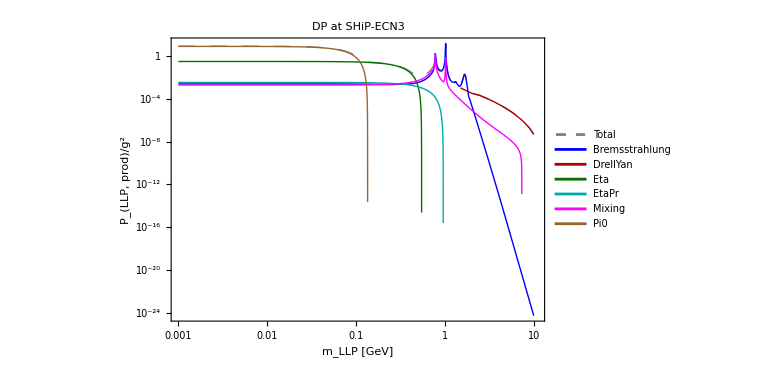

```mathematica
(*Defining the following functions:*)
(*
DoubleDistrLLPdata[proc], which is the tabulated distribution for the given production process
*)
(*
GridInFinal[process], which is Log10grids {mass, polar angle, energy} for the given tabulated distribution function
*)
(*
DistrVals[process], which are reshaped distribution values for this grid
*)
(*
PmotherToLLP[mLLP,coupling1,coupling2,process], which are interpolations of the production probabilities 
coupling1, coupling2 are two couplings controlling the production rates; for some models, there is only one coupling
*)
inecessary={};
If[Length[inecessary]==0,
NotebookEvaluate[FileNameJoin[{DirectoryRoutinesEventCalc,"ProductionProbabilities.nb"}]];
inecessary={1,2,3};
]//AbsoluteTiming
Print[Row[{"List of production channels and facilities implemented for ",LLPdirName," at ", FacilitySelected,":"}]]
ListProcesses
productionlist=Join[{"All"},ListProcesses];
DynamicModule[{choice={"All"},list,phrase},
DialogInput[Column[{Row[{"Select the production channels to be used for the sensitivity calculation:"}],Pane[TogglerBar[Dynamic[choice],productionlist,Appearance->{Automatic,Automatic}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["Submit",DialogReturn[{ProdChannelsSelected}={choice}],ImageSize->Automatic]}]]];
If[MemberQ[ProdChannelsSelected,"All"],ProdChannelsSelected=ListProcesses;]
Print["Selected production channels:"]
ProdChannelsSelected
Print["If there are production probabilities to all available distributions:"];
If[LLPdirName!="HNL",
IfCondDistrToWeights=ProdChannelsSelected==Select[WeightsCombinations,MemberQ[ProdChannelsSelected,#]&]
,
IfCondDistrToWeights=Sort[ProdChannelsSelected]==Sort[Select[DeleteDuplicates[WeightsCombinations[[All,2]]],MemberQ[ProdChannelsSelected,#]&]]
]
Do[
ProbabilityProcess[mLLP_,coupling1_,coupling2_,proc]=MotherFraction[proc]*PmotherToLLP[mLLP,coupling1,coupling2,proc]
,{proc,ProdChannelsSelected}]
If[LLPdirName=="HNL",
MixingPatternShortened=ToString[NumberForm[#,{Infinity,2}]]&/@MixingPattern;
rowprodprob=Row[{LLPdirName," with mixing pattern = ",MixingPatternShortened," at ",GivenExperiment}];
,
rowprodprob=Row[{LLPdirName," at ",GivenExperiment}];
]
{mLLPminSelected,mLLPmaxSelected}={Min[mLLPmin[#]&/@ProdChannelsSelected],Max[mLLPmax[#]&/@ProdChannelsSelected]};
(*Total LLP's production probability defined as Subscript[N, prod,total]/Subscript[N, PoT]*)
ProbabilityLLPprodTot[mLLP_,coupling1_,coupling2_]=Sum[ProbabilityProcess[mLLP,coupling1,coupling2,proc],{proc,ProdChannelsSelected}];
ptprodprob=Quiet[LogLogPlot[Evaluate[Join[{ProbabilityLLPprodTot[mLLP,1,1]},Table[ProbabilityProcess[mLLP,1,1,proc],{proc,ProdChannelsSelected}]]],{mLLP,mLLPminSelected,mLLPmaxSelected},Frame->True,ImageSize->Large,PlotLegends->Placed[Style[#,16]&/@Join[{"Total"},ProdChannelsSelected],{0.23,0.32}], FrameStyle->Directive[Black, 25],PlotRange->{{mLLPminSelected,1.1mLLPmaxSelected},All},PlotStyle->{{Thick,Gray,Dashing[0.02]},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Brown}},AspectRatio->0.66,ImageSize->Large,FrameLabel->{"m_LLP [GeV]","P_(LLP, prod)/g^2"},PlotLabel->Style[rowprodprob,16,Black],PlotPoints->200]]
```

#### Gluing distributions for all production channels

```mathematica
(*Defining the following functions*)
(*
DistrMapperMassProd[mLLP,ProdChannel], that maps the tabulated distribution {mass,theta,energy,distr} on the given mass for the given production channel
*)
(*
DistrMapperMass[mLLP,coupling1, coupling2,listprocesses], that maps the tabulated distribution {mass,theta,energy,distr} averaged over the list of the production channels `listprocesses` on the given mass
*)
(*
DistrMapper[mlist,coupling1, coupling2,listprocesses], that maps the tabulated distribution {mass,theta,energy,distr} averaged over the list of the production channels `listprocesses` on the given mass list mlist
*)
(*
FindingEmaxθ[mLLP,process,order], that returns the list {θ, Subscript[E, max](θ)} for the given LLP mass and the production channel. The parameter `order` defines Subscript[E, max]: 1-Subscript[CDF, distr](Subscript[E, max],θ) = 10^-order
*)
inecessary={};
If[Length[inecessary]==0,
NotebookEvaluate[FileNameJoin[{DirectoryRoutinesEventCalc,"DistrMapper.nb"}]];
inecessary={1,2,3};
]//AbsoluteTiming
```

List of polar angles (in rad) for final tabulated distribution:

List of energies (in GeV) for final tabulated distribution:

{3.94896,Null}

### LLP’s decays

```mathematica
(*__________________________*)
(*Defines the following functions*)
(*cτLLP[mass,coupling] - cτ of the LLP in meters*)
(*ListProcessesLLP - list of all implemented decay channels*)
(*ListBrRatios[LLPdirName,mLLP,process] - branching ratio for the given process `process` (from `ListProcessesLLP`)*)
(*PhaseSpacePerDecay[LLP,mLLP,ListDecays,Nevents,HadronizationOption,DecayUnstable] - the block simulating phase space for the given LLP with particular mass `mLLP`, averaging over the list of decays specified by `ListDecays`. The partons are hadronized if HadronizationOption = "True" (not supported yet). Unstable decay products are decayed if `DecayUnstable` = True*)
inecessary={};
If[Length[inecessary]==0,
NotebookEvaluate[FileNameJoin[{DirectoryRoutinesEventCalc,"DecayProductsSampler.nb"}]];
inecessary={1,2,3};
]//AbsoluteTiming
Print["List of all implemented decay channels:"]
ListProcessesLLP
decaylist=Join[{"All"},ListProcessesLLP];
DynamicModule[{choice={"All"},list,phrase},
DialogInput[Column[{Row[{"Select the production channels to be used for the sensitivity calculation:"}],Pane[TogglerBar[Dynamic[choice],decaylist,Appearance->"Vertical"->{Automatic,Automatic}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["Submit",DialogReturn[{ListDecaysLLPselected}={choice}],ImageSize->Automatic]}]]];
If[MemberQ[ListDecaysLLPselected,"All"],ListDecaysLLPselected=ListProcessesLLP;]
Print["List of selected decay channels:"]
ListDecaysLLPselected
PhaseSpacePerDecayFinal[mLLP_,Nevents_,HadronizationOption_,DecayUnstable_]:=PhaseSpacePerDecay[LLPdirName,mLLP,ListDecaysLLPselected,Nevents,HadronizationOption,DecayUnstable]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{27.6621,Null}

List of all implemented decay channels:

{K_LK_S,K^+K^-,K^+K^-π^0,K_SK^-π^+,K_SK^+π^-,π^+π^-π^0,π^+π^-π^+π^-,π^+π^-,ω_other,ϕ_other,(ρ^0)_other,π^0γ,π^+π^-π^0π^0,e-pair,μ-pair,τ-pair,Jets-uu,Jets-dd,Jets-ss,Jets-cc}

List of selected decay channels:

{K_LK_S,K^+K^-,K^+K^-π^0,K_SK^-π^+,K_SK^+π^-,π^+π^-π^0,π^+π^-π^+π^-,π^+π^-,ω_other,ϕ_other,(ρ^0)_other,π^0γ,π^+π^-π^0π^0,e-pair,μ-pair,τ-pair,Jets-uu,Jets-dd,Jets-ss,Jets-cc}

#### Plots

InterpolatingFunction::dmval: Input value {-2.99998} lies outside the range of data in the interpolating function. Extrapolation will be used.

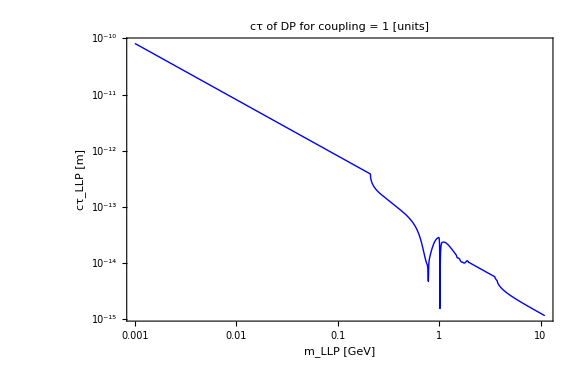

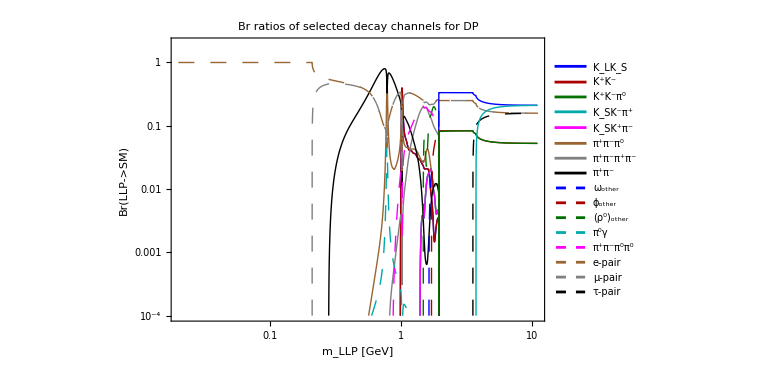

```mathematica
ptprodprob=LogLogPlot[Evaluate[cτLLP[mLLP,1]],{mLLP,mLLPminSelected,1.1mLLPmaxSelected},Frame->True,ImageSize->Large, FrameStyle->Directive[Black, 25],PlotRange->{{mLLPminSelected,1.1mLLPmaxSelected},All},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Brown}},AspectRatio->0.66,ImageSize->Large,FrameLabel->{"m_LLP [GeV]","cτ_LLP [m]"},PlotLabel->Style[Row[{"cτ of ", LLPdirName," for coupling = 1 [units]"}],20,Black],PlotPoints->200]

prdecaybrs=LogLogPlot[Evaluate[Max[ListBrRatios[LLPdirName,mLLP,#],10^-5]&/@ListDecaysLLPselected],{mLLP,Max[mLLPminSelected,0.02],1.1mLLPmaxSelected},Frame->True,ImageSize->Large, FrameStyle->Directive[Black, 25],PlotRange->{{Max[mLLPminSelected,0.02],1.1mLLPmaxSelected},{10^-4,2}},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Brown},{Thick,Gray},{Thick,Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Brown,Dashing[0.02]},{Thick,Gray,Dashing[0.02]},{Thick,Black,Dashing[0.02]}},AspectRatio->0.66,ImageSize->Large,FrameLabel->{"m_LLP [GeV]","Br(LLP->SM)"},PlotLabel->Style[Row[{"Br ratios of selected decay channels for ", LLPdirName}],20,Black],PlotPoints->200,PlotLegends->Placed[Style[#,16]&/@Join[ListDecaysLLPselected],Right]]
```

## Sampling events

## Sampling 4-momenta of the LLPs

```mathematica
(*Defining the following functions*)
(*
KinematicsFromTabulatedDistribution[mLLP,coupling1,coupling2,Nevents,cτ] - takes the tabulated distribution {θ,E,distr} as an input, samples from it Subscript[N, events] values {Subscript[θ, LLP],Subscript[E, LLP]} in the range (Subscript[θ, min,experiment],Subscript[θ, max,experiment]). Uses the function EmaxMapperMassToDecayTot to sample only the relevant energy range for the given polar angles. Also, takes into account that for small lifetimes the decay probability is not exponentially suppressed only for sufficiently large LLPs' energies. So effectively, for the given polar angle Subscript[θ, rand], the energies are sampled from some Subscript[E, min] for which Subscript[P, decay] is not too suppressed and to Subscript[E, max possible](Subscript[θ, rand])
*)
(*
LLPyieldθ[mLLP,coupling1,coupling2,θmin,θmax,Emin,Emax] - quickly calculates the amount of LLPs with mass mLLP flying in the angular domain {Subscript[θ, min],Subscript[θ, max]} and having energies within {Subscript[E, min],Subscript[E, max]}. In general, it is controlled by two production couplings. In case of particles that have only 1 production couplings, their values are not relevant
*)
(*
Momenta[pts,-Pi,Pi] - evalutes the 4-momenta given `pts` generated by KinematicsFromTabulatedDistribution. The 4-momenta are fixed in a way such that the LLP's trajectory intersects the decay volume  
*)
inecessary={};
If[Length[inecessary]==0,
NotebookEvaluate[FileNameJoin[{DirectoryRoutinesEventCalc,"LLPkinematicsSampler.nb"}]];
inecessary={1,2,3};
]//AbsoluteTiming
(*KinematicsFromTabulatedDistribution[datatest,"SPS",mLLPtest,θmintest,θmaxtest,Neventstest,EmaxMapperMassToDecay]*)
```

{13.6944,Null}

## Sampling decay vertices of the LLPs

```mathematica
(*Defining the following functions*)
(*EventBlockFinal[mLLP,coupling1,coupling2,Nev,cτ] - samples 4-momenta of LLPs in the direction of the decay volume, decay vertices inside it from the value of cτ, together with computing the yield of LLPs flying to the decay volume and the azimuthal acceptance defined for the given decay vertex (it depends on Subscript[θ, decay], Subscript[z, decay])*)
(*SimulateFullEvent[mLLP,coupling1,coupling2,Nev,cτ,HadronizationOption,DecayUnstable] - includes the output from EventBlockFinal[mLLP,coupling1,coupling2,Nev,cτ] plus the simulated phase space of the decay products, as described in the previous section*)
inecessary={};
If[Length[inecessary]==0,
NotebookEvaluate[FileNameJoin[{DirectoryRoutinesEventCalc,"DecayVerticesSampler.nb"}]];
inecessary={1,2,3};
]//AbsoluteTiming
Print["Meanings of columns of the output data for LLP:"]
{{"Column index",indexpx,indexpy,indexpz,indexenergy,indexmass,indexcθ,indexptom,indexpdec,indexxdec,indexydec,indexzdec,indexazacc,indexnprodtot,indexyield},{"Meaning","(p_(LLP, x))/GeV","(p_(LLP, y))/GeV","(p_(LLP, z))/GeV","E_LLP/GeV","m_LLP/GeV","cos(θ_LLP)","p_LLP/m_LLP","P_decay","x_dec","y_dec","z_dec","ϵ_az","N_(prod, tot)","ϵ_geom"}}//TableForm
Print["Meanings of columns of the output data for decay products (each decay product corresponds to its 8 columns):"]
{{"Column index",indexpx1,indexpy1,indexpz1,indexE1,indexm1,indexpdg1,indexcharge1,indexstability1},{"Meaning","(p_(decay product, x))/GeV","(p_(decay product, y))/GeV","(p_(decay product, z))/GeV","(E_(decay product))/GeV","(m_(decay product))/GeV","pdg_(decay product)","electric charge_(decay product)","stability_(decay product)"}}//TableForm
```

{5.19966,Null}

Meanings of columns of the output data for LLP:

Column index | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
Meaning | (p_(LLP, x))/GeV | (p_(LLP, y))/GeV | (p_(LLP, z))/GeV | E_LLP/GeV | m_LLP/GeV | cos(θ_LLP) | p_LLP/m_LLP | P_decay | x_dec | y_dec | z_dec | ϵ_az | N_(prod, tot) | ϵ_geom

Meanings of columns of the output data for decay products (each decay product corresponds to its 8 columns):

Column index | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Meaning | (p_(decay product, x))/GeV | (p_(decay product, y))/GeV | (p_(decay product, z))/GeV | (E_(decay product))/GeV | (m_(decay product))/GeV | pdg_(decay product) | electric charge_(decay product) | stability_(decay product)

## Number of events

```mathematica
NeventsBlock[mass_,coupling1_,coupling2_,Nevents_]:=Module[{c1,c2,m1},
{llpinfodata,decayproductsdata}=SimulateFullEvent[mt,coupling1val,coupling2val,Nevents];
(*Computing the number of events with decays of LLPs*)
NeventsVal=NeventsLLP[llpinfodata];
(*Converting the parameters to strings*)
{c1,c2}=ToString[ScientificForm[N[#],NumberFormat->(Row[{#1,"e",#3}]&)]]&/@{coupling1,coupling2};
m1=(mass//CForm//ToString);
Export[FileNameJoin[{NotebookDirectory[],"Sampled Nevents",GivenExperiment,LLPdirName,"DecayEvents_mass="<>m1<>"_coupling1="<>c1<>"_coupling2="<>c2<>".mx"}],decayproductsdata,"MX"];
Export[FileNameJoin[{NotebookDirectory[],"Sampled Nevents",GivenExperiment,LLPdirName,"LLPinfo_mass="<>m1<>"_coupling1="<>c1<>"_coupling2="<>c2<>".mx"}],llpinfodata,"MX"];
{NeventsVal,llpinfodata,decayproductsdata}
]
```

### Test

{5.85007,Null}

{1,1}

-Graphics3D-

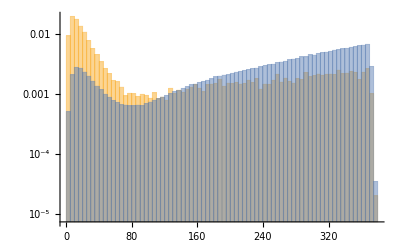

```mathematica
mt=0.9;
coupling1val=9.4*10^-17;
coupling2val=0.;
{NeventsVal,llpinfodata,decayproductsdata}=NeventsBlock[mt,coupling1val,coupling2val,10^6];//AbsoluteTiming
(*____________________*)
(*Plot decay vertices and energies distributions*)
(*____________________*)
DecPos=llpinfodata[[All,{indexxdec,indexydec,indexzdec}]];
ifinside=IfLLPinsideDecVol@@@DecPos[[All,{3,1,2}]];
ifinside//MinMax
energies=llpinfodata[[All,4]];
wts=llpinfodata[[All,indexpdec]]*llpinfodata[[All,indexazacc]];
TruePos=RandomChoice[wts->DecPos,10^4];
TrueEn=RandomChoice[wts->energies,10^4];
{xminmaxplot,yminmaxplot,zminmaxplot}=(DecPos[[All,#]]//MinMax)&/@{1,2,3};
zminmaxplot=zminmaxplot+{-1,1}Min[1,(zminmaxplot[[2]]-zminmaxplot[[1]])/10];
Show[ListPointPlot3D[TruePos,PlotStyle->{{Thickness[0.01],Blue}}],plotExperiment,PlotRange->{xminmaxplot,yminmaxplot,zminmaxplot}]
Histogram[{TrueEn,energies},100,"ProbabilityDensity",PlotRange->All,ScalingFunctions->{"Linear","Log"}]
```